```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
lin = Solve[x+a == b, x]
```

{{x→-a+b}}

```mathematica
Expand[x^2/.lin]
```

{a^2-2 a b+b^2}

```mathematica
x^2/.lin/.{a->3, b->5}
```

{4}

```mathematica
quad = Solve[a*x^2+b*x+c ==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
q1 = quad[[1]]
```

{x→(-b-√(b^2-4 a c))/(2 a)}

```mathematica
q2 = quad[[2]]
```

{x→(-b+√(b^2-4 a c))/(2 a)}

```mathematica
Solve[a*x+b*y == c && d*x+e*y == f, {x,y}]
```

{{x→-(c e-b f)/(b d-a e),y→-(-c d+a f)/(b d-a e)}}

```mathematica
Solve[x^2+y^2 == R^2 && a*x+b*y == 0, {x,y}]
```

{{x→-(b R)/(√(a^2+b^2)),y→(a R)/(√(a^2+b^2))},{x→(b R)/(√(a^2+b^2)),y→-(a R)/(√(a^2+b^2))}}

```mathematica
%/.{R->1, a->1, b->1}
```

{{x→-1/(√2),y→1/(√2)},{x→1/(√2),y→-1/(√2)}}

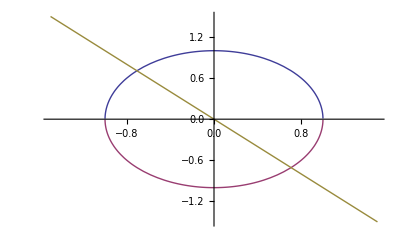

```mathematica
Plot[{√(1-x^2), -√(1-x^2), -x},{x,-1.5,1.5}]
```

```mathematica
FindRoot[{x^2+y^2==1, x+y==0},{x,1},{y,-1}]
```

{x→0.707107,y→-0.707107}

```mathematica
FindRoot[{x^2+y^2==1, x+y==0},{x,-1},{y,1}]
```

{x→-0.707107,y→0.707107}

```mathematica
N[1/√2]
```

0.707107

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,25]
```

3.141592653589793238462643

```mathematica
N[E,10]
```

2.718281828

```mathematica
eq1 = (x/a)^2+(y/b)^2 == 1;
eq2 = c*x + d*y == 1;
abcd = {a->1, b->2, c->3, d->4};
soln = Solve[{eq1, eq2}, {x,y}]
```

{{x→(a^2 c-√(-a^2 b^2 d^2+a^4 b^2 c^2 d^2+a^2 b^4 d^4))/(a^2 c^2+b^2 d^2),y→(1-(a^2 c^2)/(a^2 c^2+b^2 d^2)+(c √(a^2 b^2 d^2 (-1+a^2 c^2+b^2 d^2)))/(a^2 c^2+b^2 d^2))/d},{x→(a^2 c+√(-a^2 b^2 d^2+a^4 b^2 c^2 d^2+a^2 b^4 d^4))/(a^2 c^2+b^2 d^2),y→(1-(a^2 c^2)/(a^2 c^2+b^2 d^2)-(c √(a^2 b^2 d^2 (-1+a^2 c^2+b^2 d^2)))/(a^2 c^2+b^2 d^2))/d}}

```mathematica
N[soln/.abcd]
```

{{x→-0.888798,y→0.916598},{x→0.97099,y→-0.478242}}

```mathematica
NSolve[{eq1, eq2}/.abcd, {x,y}]
```

{{x→-0.888798,y→0.916598},{x→0.97099,y→-0.478242}}

```mathematica
NSolve[x^5-2*x+3==0, x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
NSolve[x^5-2*x+3==0, x, Reals]
```

{{x→-1.42361}}

```mathematica
NSolve[{Sin[x]==1/3},x]
```

{{x→ConditionalExpression[1. (0.339837+6.28319 C[1]),C[1]∈Integers]},{x→ConditionalExpression[1. (2.80176+6.28319 C[1]),C[1]∈Integers]}}

```mathematica
FindRoot[Sin[x]-1/3, {x,0.3}]
```

{x→0.339837}

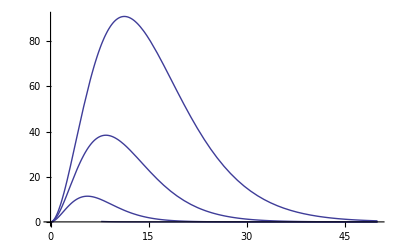

```mathematica
Show[Evaluate@Table[Plot[x^3/(Exp[x/T]-1),{x,0,50}],{T,1,4}], PlotRange->All]
```

```mathematica
x^(-5)/(Exp[1/(x*T)]-1)
```

1/((-1+ⅇ^(1/(T x))) x^5)

```mathematica
deriv = FullSimplify[D[x^(-5)/(Exp[1/(x*T)]-1),x]]
```

(5 T x+ⅇ^(1/(T x)) (1-5 T x))/((-1+ⅇ^(1/(T x)))^2 T x^7)

```mathematica
toSolve = FullSimplify[temp]/.T->1/(x*y)
```

((ⅇ^y (1-5/y)+5/y) y)/((-1+ⅇ^y)^2 x^6)

```mathematica
soln = Solve[toSolve==0,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→5+ProductLog[-5/ⅇ^5]}}

```mathematica
N[soln]
```

{{y→4.96511}}

```mathematica
Remove["Global`*"]
```

```mathematica
Table[(-1)^n/(2*n+1),{n,0,10}]
```

{1,-1/3,1/5,-1/7,1/9,-1/11,1/13,-1/15,1/17,-1/19,1/21}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]-Pi/4},{m,10,50,10}]
```

{{0.0226808},{0.011898},{0.00806242},{0.00609665},{0.00490149}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)/(4*(m+1))-Pi/4},{m,10,50,10}]
```

{{-0.0000464838},{-6.72973×10^-6},{-2.09523×10^-6},{-9.06162×10^-7},{-4.70935×10^-7}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)*(m+1)/((2*m+2)^2+1)-Pi/4},{m,10,50,10}]
```

{{3.76583×10^-7},{1.51748×10^-8},{2.17462×10^-9},{5.38262×10^-10},{1.80886×10^-10}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)*((m+1)^2+1)/((m+1)*((2*m+2)^2+5))-Pi/4},{m,10,50,10}]
```

{{-6.73298×10^-9},{-7.65623×10^-11},{-5.06528×10^-12},{-7.18314×10^-13},{-1.56097×10^-13}}

```mathematica
Remove["Global`*"]
```

```mathematica
g=9.8; v0=5; h=10;Theta=Pi/12;
x[t_] =v0*t*Cos[Theta];
y[t_] =h+v0*t*Sin[Theta]-1/2*g*t^2;
```

```mathematica
Solve[y[t]==0,t]
```

{{t→-1.30261},{t→1.56671}}

```mathematica
FindRoot[{h+v0*t*Sin[Theta]-1/2*g*t^2},{t,1}]
```

{t→1.56671}

```mathematica
Table[x[t],{t,0,2,0.1}]
Table[y[t],{t,0,1.6,0.1}]
```

{0.,0.482963,0.965926,1.44889,1.93185,2.41481,2.89778,3.38074,3.8637,4.34667,4.82963,5.31259,5.79555,6.27852,6.76148,7.24444,7.72741,8.21037,8.69333,9.1763,9.65926}

{10.,10.0804,10.0628,9.94723,9.73364,9.42205,9.01246,8.50487,7.89928,7.19569,6.3941,5.4945,4.49691,3.40132,2.20773,0.916143,-0.473448}

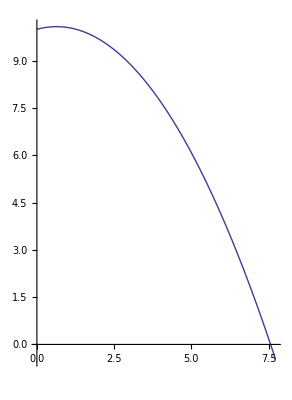

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,1.6}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
g=9.8; v0=5;
x[t_,Theta_] =v0*t*Cos[Theta];
y[t_,h_, Theta_] =h+v0*t*Sin[Theta]-1/2*g*t^2;
```

```mathematica
N[Solve[y[t,h,Theta]==0,t]/.{h->10, Theta->Pi/12}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{t→1.56671}

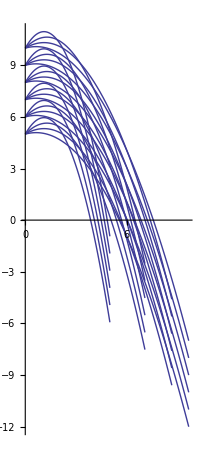

```mathematica
Show[Evaluate@Table[ParametricPlot[{x[t,Theta],y[t,h,Theta]},{t,0,2}],{h,5,10},{Theta, Pi/12,Pi/3,Pi/12}], PlotRange->All]
```

```mathematica
Manipulate[ParametricPlot[{x[t,Theta],y[t,h, Theta]},{t,0,2}],{h,5,10},{Theta, Pi/12,Pi/3,Pi/12}]
```

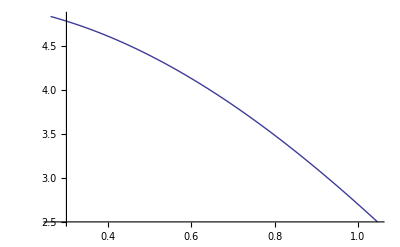

```mathematica
Show[Evaluate@Table[Plot[x[t,Theta],{Theta,Pi/12,Pi/3}],{t,1,4,1}]]
```

```mathematica
Table[x[t,Theta]/.{Theta->Pi/12},{t,FindRoot[y[t,h,Theta]/.{h->10, Theta->Pi/12},t]}]
```

FindRoot::fdss: Search specification t should be a list with 1 to 5 elements.

Table::iterb: Iterator {t, FindRoot[y[t, h, Theta]/. {h → 10, Theta → π/12}, t]} does not have appropriate bounds.

Table[x[t,Theta]/.{Theta→π/12},{t,FindRoot[y[t,h,Theta]/.{h→10,Theta→π/12},t]}]

```mathematica
Table[FindRoot[y[t,h,Theta]/.{h->10},{t,1}],{Theta,Pi/12,Pi/3,Pi/12}]
```

{{t→1.56671},{t→1.70627},{t→1.83419},{t→1.93719}}

```mathematica
Table[FindRoot[y[t,h,Theta]/.{Theta->Pi/12},{t,1}],{h,5,10,1}]
```

{{t→1.1508},{t→1.24647},{t→1.33455},{t→1.41661},{t→1.49373},{t→1.56671}}

```mathematica
x[%,Theta]/.{Theta->Pi/12}
```

{{(5 (1+√3) (t→1.1508))/(2 √2)},{(5 (1+√3) (t→1.24647))/(2 √2)},{(5 (1+√3) (t→1.33455))/(2 √2)},{(5 (1+√3) (t→1.41661))/(2 √2)},{(5 (1+√3) (t→1.49373))/(2 √2)},{(5 (1+√3) (t→1.56671))/(2 √2)}}

```mathematica
Table[NSolve[y[t,h,Pi/12]==0,t][[2]],{h,5,10,1}]
```

{{t→1.1508},{t→1.24647},{t→1.33455},{t→1.41661},{t→1.49373},{t→1.56671}}

```mathematica
x[N[%],Theta]/.{Theta->Pi/12}
```

{{(5 (1+√3) (t→1.1508))/(2 √2)},{(5 (1+√3) (t→1.24647))/(2 √2)},{(5 (1+√3) (t→1.33455))/(2 √2)},{(5 (1+√3) (t→1.41661))/(2 √2)},{(5 (1+√3) (t→1.49373))/(2 √2)},{(5 (1+√3) (t→1.56671))/(2 √2)}}

```mathematica
Plot[{x[FindRoot[y[t,h,Theta]/.{h->10},{t,1}], Theta]},{Theta,Pi,2*Pi}]
```

-Graphics-

```mathematica
Plot[x[NSolve[y[t,h,Theta]/.{Theta->Pi/12}==0,t], Theta]/.{Theta->Pi/12},{h,5,10}]
```

ReplaceAll::reps: {{Theta → π/12} == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-